# Noise and SNR analysis of camera

GUO, Zhichao

guozc12@gmail.com

Dajun Wang’s Cold Atom Lab @The Chinese University of Hong Kong

2020.06.09 - Ver_1.0
2020.10.17 - Ver_1.1
2021.04.14 - Ver_2.0

Abstract

In this note, we analyse the noise and SBR of cameras. We first introduce a general structure of camera’s noise. Then we compare different type of cameras, including CCD, CMOS and EMCCD. We try to describe their work principle to show the pro and con of them. Finally, we focus on the readout and dark-current noise of cameras. Noticed that a CCD camera will have a single value of readout noise for all pixel; However, CMOS camera have different readout noise for each pixel. Most of pixel perform excellent, except others work bad with long tail on the noise histogram. We follow Hamamatsu Optics’ suggestion, using the RMS value describe all kind of noise.

## General analysis of noise and SNR of camera

### Signal

As shown in the above figure, a typical process for a camera converting photons to the final counts on your computer is divided into two steps. First, the receiving photon is converted to electrons by a CCD or CMOS. In this process, we use quantum efficiency(QE) to characterize it, i.e.

N_electron=QE×N_photon

Then, in the second step, electrons are converted to digital signal (i.e N_count or ADU) by a ADC, where typical characterization is the so-called ADC efficiency (or Gain in some manufacture, such as FLIR)

N_count=N_electron/ADC

where the unit of ADC is e^-/ADU, which means for a unit change in the counts how many electrons are needed. So, large ADC value renders less sensitivity and vice versus. Moreover, with different ADC (12bit or 14bit) there will be different ADC efficient value. Actually, you can consider 1/ADC as gain of ADC convertor, and higher bit it use, higher gain you achieve.

Combined two steps, we have

N_count=1/ADC(N_photon×QE)=Gain×(N_photon×QE)

### Noise

The noise formula is

σ_count=1/ADC √(σ_rd^2+σ_dark^2+QE×N_photon)=1/ADC √(σ_rd^2+I_dark×t+QE×N_photon)=Gain √(σ_rd^2+I_dark×t+QE×N_photon)

Here we use the standard deviation for evaluation of all kind of noise. However, if the noise distribution is not Poisson or Gaussian, this evaluation cannot reveal the true noise distribution.

σ_rd is the readout noise of camera, which is independent of the signal. A typical value for CCD is 6 e^- and for CMOS is about 2 e^-. The CCD camera suffer a worse readout noise because the transition of electron between pixels make all pixel share the same readout noise, typical 6~10 e^-.

σ_dark^2 is the dark noise of camera, which is proportional to the dark current I_dark and the exposure time t, i.e. σ_dark=√(I_dark×t). A typical value of I_dark is about 1 e^-/s. So, for a 100us level exposure time, the dark noise can be ignored.

### SNR

SNR of camera is

SNR=N_count/σ_count=(N_photon×QE)/(√(σ_rd^2+σ_dark^2+QE×N_photon))

We plot the SNR as a function of photon number with QE=0.5, σ_dark→0 and with different σ_rd

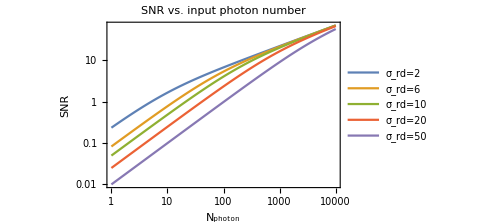

We can see that for large photon, actually better read noise improve very little. However, for small photon, better readout noise can perform better.

We compare the ratio of SNR between σ_rd=2 and σ_rd=6, which is our case for BlackFly CMOS camera to Point-gray CCD.

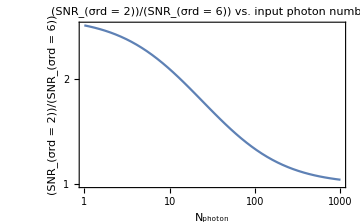

```mathematica
LogLogPlot[((Np×QE)/(√(Subscript[σ, rd]^2+Subscript[σ, dark]^2+QE×Np))/.{Subscript[σ, dark]->0,QE->0.5,Subscript[σ, rd]->2})/((Np×QE)/(√(Subscript[σ, rd]^2+Subscript[σ, dark]^2+QE×Np))/.{Subscript[σ, dark]->0,QE->0.5,Subscript[σ, rd]->6}),{Np,1,1000},Frame->True,PlotLegends->Automatic,PlotLabel->Style["(SNR_(σrd = 2))/(SNR_(σrd = 6)) vs. input photon number",FontSize->20],FrameLabel->{Style["N_photon",FontFamily->"Times New Roman",FontSize->20],Style["(SNR_(σrd = 2))/(SNR_(σrd = 6))",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]
```

We can see the improvement only happens when photon number less than 100.

In the following table, we list the parameters of above analysis.

## Comparison: CCD, CMOS, and EMCCD

### CCD v.s. CMOS camera

-Graphics-

(Ref: https://www.gatan.com/ccd-vs-cmos)

##### CCD camera signal process

Photon hits pixel sensor generating electron.

Electrons transferred to "amplifier"; really a capacitor. Units are coulombs.

The voltage induced by this charge is measured. Units are volts.

An Analog-To-Digital (A/D) unit converts the voltage into some other voltage, which may have only one of several discrete levels. Units are still volts.

The voltage is converted into a number which is passed from the hardware to the computer software as the pixel's value. Units are counts, also called "Data Numbers" (DN) or "Analog-to-Digital Units" (ADUs).

##### CMOS camera signal process

Photons hit the sensor and generate charge (electrons).

The photo-generated charge is converted to an analog voltage for each pixel amplifier.

These pixel voltages are transferred to the column bus via a row select signal.

The analog voltages are then converted to digital signals via columns of analog to digital (A/D) converters.

The final digitized signals are then read out sequentially at a pixel readout speed which normally can be set at different speeds.

##### Comparison

Because CCD use one amplifier and ADC serving for all pixel, its frame rate (speed) is limited.

For the same reason, CCD will have a single value of readout noise. However, CMOS camera will have DIFFERENT readout noise for EACH pixel. This will be discussed in the last section.

Same as readout noise, the dark current will also differs by each pixel for CMOS camera.

### EMCCD camera

If considering the EMCCD, which means after converting photons to electrons, there is a avalanche effect there for producing additional electrons, we need to add a Gain (G_EM) into the first process, i.e.

N_count=1/ADC(N_photon×QE×G_EM)=Gain×(N_photon×QE×G_EM)

The typical value of G_EM for a EMCCD is about 1000.

Correspondingly, this gain will cause a additional noise when achieving electrons, which be characterized by the parameter called “noise factor” (F). typical value for F is about 1.4. Then we can rewrite the noise formula

σ_count=1/ADC √(σ_rd^2+F^2 G_EM^2(σ_dark^2+QE×N_photon))=Gain×√(σ_rd^2+F^2 G_EM^2(σ_dark^2+QE×N_photon))

and SNR is

SNR=N_count/σ_count=(N_photon×QE×G_EM)/(√(σ_rd^2+F^2 G_EM^2(σ_dark^2+QE×N_photon)))=N_photon/(√(σ_rd^2/G_EM^2+F^2 QE N_photon+F^2 σ_dark^2))

Thus, We can see that readout noise be suppressed a lot due to very large G_EM.

## Readout noise and Dark noise

### Distribution of readout and dark noise

As we already now well about the photon shot noise, which is a Poisson distribution, we can use the “mean” and “SD” describing it quit well. Even the only two parameters of “mean” and “SD” only reveal the distribution of a Gaussian, due to the central limit theory, Poisson distribution with large k shows really good simulation of a Gaussian.

However, what about the readout noise and dark noise? The answer is: they are not Gaussian or Poisson. As depicted in the Hamamatsu optics’ note:

“With any statistical parameter there are multiple models available to apply to the data. The classic electrical engineering method for calculating read noise is to define the root mean square (rms). This has always been the method used to calculate read noise for CCDs. Median and rms are both perfectly valid statistical models, but only rms noise accurately represents the experience that a user can expect from a camera. With CCDs there are never any issues regarding which model to use because the typical read noise for all pixels is very similar, thus rms and median are equivalent. With sCMOS, the structure of the sensor inherently has more pixel variation, and the extreme low noise of the sensor makes variation more statistically significant. So when it comes to evaluating camera performance, the truly meaningful spec is rms noise. The rms noise value provides insight into image quality as well as being the appropriate noise variable in quantitative calculations. For example, SNR measurements made empirically align with theory only when these simulations are done using rms noise values. Currently there is no industry standard in life science imaging for reporting noise specifications and it has become common practice for sCMOS to be specified by median read noise values. We include median noise data to facilitate superficial comparison with other sCMOS cameras, but we encourage users to be skeptical of median noise as a specification and to demand the more meaningful rms noise. The ORCA-Flash4.0 V2 Gen II sCMOS has 1.9 e- rms and 1.3 e- median typical read noise at standard scan.”
(Ref: https://camera.hamamatsu.com/jp/en/technical_guides/read_noise/index.html)

-Graphics-

(Ref: https://camera.hamamatsu.com/jp/en/technical_guides/read_noise/index.html)

Note here, this distribution is caused by different noise on each pixel, thus cannot formulated as a single number as CCD.

As recommended by Hamamatsu optics, standard deviation is a better choice for evaluating the quality of a image. Thus, Here we choose all noise as SD type (RMS type) for CMOS camera.

##### Test data: BF-31S4 CMOS camera noise

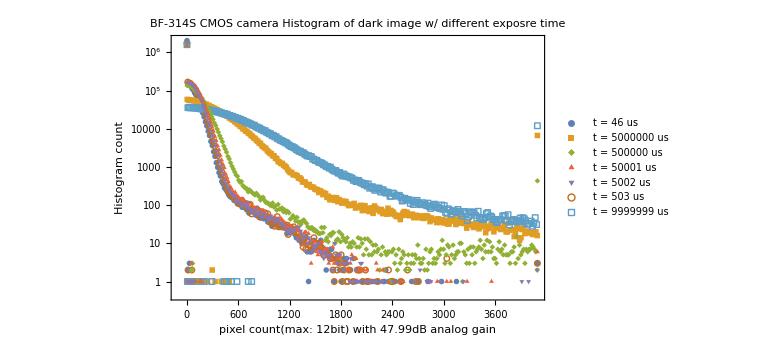

## References

CCD, EMCCD and ICCD comparing (https://andor.oxinst.com/learning/view/article/ccd,-emccd-and-iccd-comparisons)

CCD v.s. CMOS: https://www.gatan.com/ccd-vs-cmos

Old note on CCD: https://www.phys.hawaii.edu/~bellepix/hv/bib/CCD&Reduccion_p1.pdf

CMOS camera: https://andor.oxinst.com/learning/view/article/understanding-read-noise-in-scmos-cameras

Readout noise distribution:  https://camera.hamamatsu.com/jp/en/technical_guides/read_noise/index.html

More information of camera noise can be found in HAMAMATSU website (other tag): https://camera.hamamatsu.com/jp/en/technical_guides/read_noise/index.html

Camera Noise and Temperature Tutorial (https://www.thorlabs.com/newgrouppage9.cfm?objectgroup_id=10773)